```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
?Mesh
```

Mesh is an option for Plot3D, DensityPlot, and other plotting functions that specifies what mesh should be drawn.

```mathematica
?Lighter
```

RowBox[{"Lighter", "[", StyleBox["color", "TI"], "]"}] represents a lighter version of the specified color. 
RowBox[{"Lighter", "[", RowBox[{StyleBox["color", "TI"], ",", StyleBox["f", "TI"]}], "]"}] represents a version of the specified color lightened by a fraction StyleBox["f", "TI"]. 
RowBox[{"Lighter", "[", RowBox[{StyleBox["image", "TI"], ",", StyleBox["…", "TR"]}], "]"}] gives a lighter version of an image.

```mathematica
?Filling
```

Filling is an option for ListPlot, Plot, Plot3D, and related functions that specifies what filling to add under points, curves, and surfaces.

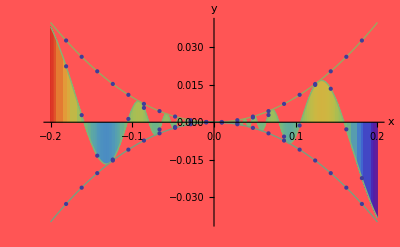

```mathematica
Plot[{x^2*Sin[1/x],x^2,-x^2}, {x,-.2,.2},Filling -> {1->Axis}, ColorFunction -> "Rainbow", PlotStyle -> Thick, Mesh->20, Background -> Lighter[Red], AxesLabel -> {x,y}]
```

```mathematica
Plot3D[Sin[x]*y, {x,-10,10},{y,-10,10}]
```

-Graphics3D-

```mathematica
Options[Plot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,AutomaticImageSize→False,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClippingStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Opacity[0.5],FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,SphericalRegion→False,TextureCoordinateFunction→Automatic,TextureCoordinateScaling→Automatic,Ticks→Automatic,TicksStyle→{},ViewAngle→Automatic,ViewCenter→Automatic,ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

```mathematica
?Manipulate
```

Manipulate[expr,{u,u_min,u_max}] generates a version of expr with controls added to allow interactive manipulation of the value of u. 
Manipulate[expr,{u,u_min,u_max,du}] allows the value of u to vary between u_min and u_max in steps du. 
Manipulate[expr,{{u,u_init},u_min,u_max,…}] takes the initial value of u to be u_init. 
Manipulate[expr,{{u,u_init,u_lbl},…}] labels the controls for u with u_lbl. 
Manipulate[expr,{u,{u_1,u_2,…}}] allows u to take on discrete values u_1,u_2,…. 
Manipulate[expr,{u,…},{v,…},…] provides controls to manipulate each of the u,v,…. 
Manipulate[expr,c_u->{u,…},c_v->{v,…},…] links the controls to the specified controllers on an external device.

```mathematica
Manipulate[
Plot[
{x^a*Sin[1/(a*x)],x^a,-x^a}, {x,-domain,domain},
Filling -> {1->Axis}, 
ColorFunction -> "Rainbow", 
PlotStyle -> Thick, Mesh->mesh, 
Background -> Lighter[Red, lighter], 
AxesLabel -> {x,y}],
{a,1,10},{b,0,4}, {mesh,1,10,1}, {lighter, 0, 1},{domain, 0.01, 1}
]
```

```mathematica
Manipulate[ParametricPlot[{u*Cos[u +d],u*Sin[u+d]},{u,0.1,2π}],{d,0,Pi}]
```

```mathematica
?Part
```

expr[[i]] or Part[expr,i] gives the i^th part of expr. 
expr[[-i]] counts from the end. 
expr[[i,j,…]] or Part[expr,i,j,…] is equivalent to expr[[i]][[j]]…. 
expr[[{i_1,i_2,…}]] gives a list of the parts i_1, i_2, … of expr. 
expr[[m;;n]] gives parts m through n.
expr[[m;;n;;s]] gives parts m through n in steps of s.

```mathematica
?Graphics3D
```

Graphics3D[primitives,options] represents a three-dimensional graphical image.

```mathematica
?PolyhedronData
```

PolyhedronData[poly,property] gives the value of the specified property for the polyhedron named poly.
PolyhedronData[poly] gives an image of the polyhedron named poly.
PolyhedronData[class] gives a list of the polyhedra in the specified class.

```mathematica
Manipulate[PolyhedronData["Part[PolyhedronData[p],1]"],{p,4,20,1}]
```

PolyhedronData::notdef: PolyhedronData has no value associated with the specified argument(s).

```mathematica
Manipulate[PolyhedronData[Part[PolyhedronData[p],1]], {p,4,100,1}]
```

```mathematica
poly = PolyhedronData[28];
If[MatchQ[poly, {}],
"I don't know!",
poly[[1]]
]
```

I don't know!

```mathematica
?Part
```

expr[[i]] or Part[expr,i] gives the i^th part of expr. 
expr[[-i]] counts from the end. 
expr[[i,j,…]] or Part[expr,i,j,…] is equivalent to expr[[i]][[j]]…. 
expr[[{i_1,i_2,…}]] gives a list of the parts i_1, i_2, … of expr. 
expr[[m;;n]] gives parts m through n.
expr[[m;;n;;s]] gives parts m through n in steps of s.

```mathematica
PolyhedronData[44]
```

{}

```mathematica
Functions!!!
```

```mathematica
FunctionName[x_] := x + 5
FunctionName[30]
```

35

```mathematica
Half[x_] := x/2
```

```mathematica
Half[20]
```

10

```mathematica
quotient[x_,y_]:=x/y
```

```mathematica
quotient[1,2]
```

1/2

```mathematica
five[x_]:= 5
```

```mathematica
five[20]
```

5

```mathematica
five[_]:= 5
```

```mathematica
five[5656565]
```

5

```mathematica
five[_,_]:=5.5 (*<- Down Value*)
```

```mathematica
five[5,67]
```

5.5

```mathematica
five[6]
```

5

```mathematica
Clear[five]
```

```mathematica
Six[__]:=6
```

```mathematica
Six[1,2,3,4,5,6,7,8,9,10,12,12,13,14,151,61,71,1,7,1,717,17,17,1]
```

```mathematica
6
Six[1,2]
```

6

6

```mathematica
Six[]
```

Six[]

```mathematica
Seven[___]:=7
```

```mathematica
Seven[1]
```

7

```mathematica
Seven[1,2,3,4,5,6]
```

7

```mathematica
Seven[]
```

7

```mathematica
Add[x_,y_,z_]:=x+y+z
```

```mathematica
Add[x_,y_]:=x+y
```

```mathematica
Add[1,2,3]
```

6

```mathematica
Add[1,2]
```

3

```mathematica
?Sequence
```

Sequence[expr_1,expr_2,…] represents a sequence of arguments to be spliced automatically into any function.

```mathematica
list[x__]:=List[x]
sequence[x__]:= x
```

```mathematica
sequence[2]
```

2

```mathematica
sequence[1,2,3,4,5]
```

Sequence[1,2,3,4,5]

```mathematica
list[sequence[1,2,3,4,5,6,7,8,9,0]]
```

{1,2,3,4,5,6,7,8,9,0}

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,{1}] or f@@@expr replaces heads at level 1 of expr by f.
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec.

```mathematica
factorial[n_]:=
Times[
Apply[
Sequence,
Table[j,{j,1,n}]
]
]
```

```mathematica
factorial[3]
```

6

```mathematica
function[x__]:=
```

```mathematica
?Transpose
```

Transpose[list] transposes the first two levels in list. 
Transpose[list,{n_1,n_2,…}] transposes list so that the k^th level in list is the n_k^th level in the result.

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,{1}] or f@@@expr replaces heads at level 1 of expr by f.
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec.

```mathematica
Apply[Plus, List[1,2,3]]
```

6

```mathematica
Sequence[1,2,3]
Plus[2,3,4]
```

Sequence[1,2,3]

9

```mathematica
Head[4]
```

Integer

```mathematica
Apply[Plus,4]
```

4

```mathematica
Head[Sqrt[-1]]
```

Complex

```mathematica
j
```

j

```mathematica
factorial[x_]:=Apply[Times,Table[i,{i,x}]]
```

```mathematica
factorial[18]
```

6402373705728000

```mathematica
Manipulate[Table[factorial[i],{i,1,x,1}],{x,1,100}]
```

Set::setraw: Cannot assign to raw object 3.

General::stop: Further output of Set :: setraw will be suppressed during this calculation.

Set::setraw: Cannot assign to raw object 1.

Set::setraw: Cannot assign to raw object 2.

Set::setraw: Cannot assign to raw object 3.

General::stop: Further output of Set :: setraw will be suppressed during this calculation.

```mathematica
factorial[x_]:=If[x==1,1,x*factorial[x-1]]
```

```mathematica
factorial2[x_?IntegerQ]:=x*factorial2[x-1]
factorial2[1]:=1
```

```mathematica
factorial2[255]
```

3350850684932979117652665123754814942022584063591740702576779884286208799035732771005626138126763314259280802118502282445926550135522251856727692533193070412811083330325659322041700029792166250734253390513754466045711240338462701034020262992581378423147276636643647155396305352541105541439434840109915068285430675068591638581980604162940383356586739198268782104924614076605793562865241982176207428620969776803149467431386807972438247689158656000000000000000000000000000000000000000000000000000000000000000

```mathematica
Five[x_]:=(
x+7;
x+6;
x+92;
Row[{x,x+6},","])
```

```mathematica
fib[x_]:=fib[x]=fib[x-1]+fib[x-2]
fib[1]=1;
fib[2]=1;
```

```mathematica
?Cases
```

RowBox[{"Cases", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["e", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["pattern", "TI"]}], "]"}] gives a list of the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["e", "TI"], StyleBox["1", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{StyleBox["pattern", "TI"], "->", StyleBox["rhs", "TI"]}]}], "]"}] gives a list of the values of StyleBox["rhs", "TI"] corresponding to the SubscriptBox[StyleBox["e", "TI"], StyleBox["i", "TI"]] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"]}], "]"}] gives a list of all parts of StyleBox["expr", "TI"] on levels specified by StyleBox["levelspec", "TI"] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{StyleBox["expr", "TI"], ",", RowBox[{StyleBox["pattern", "TI"], "->", StyleBox["rhs", "TI"]}], ",", StyleBox["levelspec", "TI"]}], "]"}] gives the values of StyleBox["rhs", "TI"] that match the pattern. 
RowBox[{"Cases", "[", RowBox[{StyleBox["expr", "TI"], ",", StyleBox["pattern", "TI"], ",", StyleBox["levelspec", "TI"], ",", StyleBox["n", "TI"]}], "]"}] gives the first StyleBox["n", "TI"] parts in StyleBox["expr", "TI"] that match the pattern.

```mathematica
fib[746]
```

fib[746]

```mathematica
Manipulate[Table[fib[x],{x,1,i}],{i,1,1000,1}]
```

```mathematica
?Select
```

Select[list,crit] picks out all elements e_i of list for which crit[e_i] is True. 
Select[list,crit,n] picks out the first n elements for which crit[e_i] is True.

```mathematica
?Map
```

Map[f,expr] or f/@expr applies f to each element on the first level in expr. 
Map[f,expr,levelspec] applies f to parts of expr specified by levelspec.

```mathematica
?ReplaceAll
```

expr/.rules applies a rule or list of rules in an attempt to transform each subpart of an expression expr.

## FUN TIME

```mathematica
PCOwners={"Total"-> 17,"MyChoice"-> 7,"ParentsChoice"-> 14}
MacOwners={"Total" -> 10}
BothOwners={"Total"-> 5}
```

{Total→17}

{Total→10}

{Total→5}

```mathematica
?BarChart
```

BarChart[{y_1,y_2,…}] makes a bar chart with bar lengths y_1,  y_2, ….
BarChart[{…,w_i[y_i,…],…,w_j[y_j,…],…}] makes a bar chart with bar features defined by the symbolic wrappers w_k.
BarChart[{data_1,data_2,…}] makes a bar chart from multiple datasets data_i.

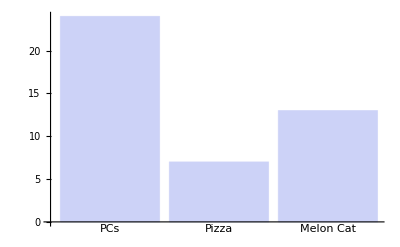

```mathematica
BarChart[{24,7,13},ChartLabels-> {"PCs","Pizza","Melon Cat"}]
```

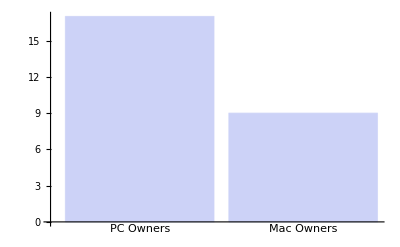

```mathematica
BarChart[{17,9},ChartLabels-> {"PC Owners","Mac Owners"}]
```

```mathematica
Map[ReplaceAll["Total",#]&,{PCOwners,MacOwners}]
```

{17,5}

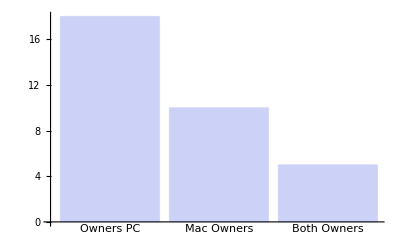

```mathematica
BarChart[Map[ReplaceAll["Total",#]&,{PCOwners,MacOwners, BothOwners}],ChartLabels-> {PC Owners, Mac Owners, Both Owners}]
```

```mathematica
PCOwners={
"Total"-> 18,
"TwoPCs"-> 5,
"MyChoice"-> 8,
"ParentsChoice"-> 15};
MacOwners={
"Total"-> 10,
"TwoMacs"-> 0,
"MyChoice"-> 3,
"ParentsChoice"-> 7}
```

{Total→10,TwoMacs→0,MyChoice→3,ParentsChoice→7}

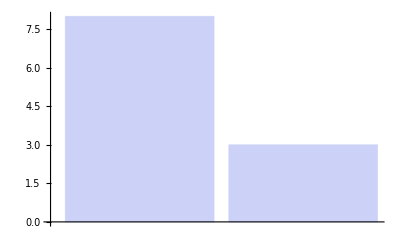

```mathematica
BarChart[Map[ReplaceAll["MyChoice",#]&,{PCOwners,MacOwners}]]
```

```mathematica
Map[ReplaceAll["MyChoice",#]&,{PCOwners,MacOwners}]
```

{8,3}

```mathematica
Plus@@Map[ReplaceAll["MyChoice",#]&,{PCOwners,MacOwners}]
(*Replaces List with Plus*)
```

11

```mathematica
Plus@@Map[ReplaceAll["ParentsChoice",#]&,{PCOwners,MacOwners}]
(*Replaces List with Plus*)
```

22

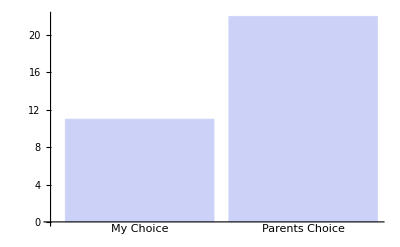

```mathematica
BarChart[
{Plus@@Map[ReplaceAll["MyChoice",#]&,{PCOwners,MacOwners}],
Plus@@Map[ReplaceAll["ParentsChoice",#]&,{PCOwners,MacOwners}]}
,
ChartLabels-> {"My Choice","Parents Choice"}
]
```

```mathematica
iPhoneOwners={
"Name"-> "iPhone",
"Total"-> 5,
"MyChoice"-> 1,
"ParentsChoice"-> 4,
};
BlackBerryOwners={
"Name"-> "BlackBerry",
"Total"-> 1,
"MyChoice"-> 1,
"ParentsChoice"-> 0
};
AndroidOwners={
"Name"-> "Android",
"Total"-> 5,
"MyChoice"-> 4,
"ParentsChoice"-> 1
};
WindowsOwners={
"Name"-> "Windows",
"Total"-> 1,
"MyChoice"-> 1,
"ParentsChoice"-> 0
};
OtherOwners={
"Name"-> "Other",
"Total"-> 9,
"MyChoice"-> 4,
"ParentsChoice"-> 5
};
NoPhoneOwners={
"Name"-> "None",
"Total"-> 1,
"MyChoice"-> 1,
"ParentsChoice"->0 
};
```

```mathematica
?PieChart
```

PieChart[{y_1,y_2,…}] makes a pie chart with sector angle proportional to y_1, y_2, ….
PieChart[{…,w_i[y_i,…],…,w_j[y_j,…],…}] makes a pie chart with sector features defined by the symbolic wrappers w_k.
PieChart[{data_1,data_2,…}] makes a pie chart from multiple datasets data_i.

```mathematica
PieChart[Map[ReplaceAll["Total",#]&,{iPhoneOwners,BlackBerryOwners,AndroidOwners,WindowsOwners,OtherOwners,NoPhoneOwners}],ChartLabels-> Map[ReplaceAll["Name",#]&,{iPhoneOwners,BlackBerryOwners,AndroidOwners,WindowsOwners,OtherOwners,NoPhoneOwners}]]
```

-Graphics-

```mathematica
Map[ReplaceAll["MyChoice",#]&, iPhoneOwners]
```

ReplaceAll::reps: {Null} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{MyChoice,MyChoice,1,MyChoice,MyChoice/.Null}

```mathematica
AllPhoneKinds
```

```mathematica
?EventHandler
```

EventHandler[expr,{event_1:>action_1,event_2:>action_2,…}] displays as expr, evaluating action_i whenever "event_i" occurs in connection with expr.

```mathematica
Set Background-> Blue
```

Background Set→RGBColor[0,0,1]

```mathematica
?Notebook
```

Notebook[{cell_1,cell_2,…}] is the low-level construct that represents a notebook manipulated by the Mathematica front end.

```mathematica
NotebookSelection[nb] Background-> Blue
```

Background NotebookSelection[nb]→RGBColor[0,0,1]

```mathematica
board=ConstantArray[2,{3,3}]
```

{{2,2,2},{2,2,2},{2,2,2}}

```mathematica
Grid@board
```

2 | 2 | 2
2 | 2 | 2
2 | 2 | 2

```mathematica
turnx=True;
Grid[
MapIndexed[
Button[Switch[#1,2,"",1,"x",0,"o"],
(*Action *)
board⟦#2⟧=If[board[[2]]≠ 2,
If[turnx,1,0]
];
turnx=!turnX;

]&,
board,{2}
],
Background-> Black]
```

```mathematica
expr=x^4-6x^2+3
```

3-6 x^2+x^4

```mathematica
xsolutions=Solve[expr==0,x]
```

{{x→-√(3-√6)},{x→√(3-√6)},{x→-√(3+√6)},{x→√(3+√6)}}

```mathematica
ysolutions=Simplify[expr/.xsolutions]
```

{0,0,0,0}

```mathematica
Point/@Transpose[{xsolutions,ysolutions}]/.({x-> a_})-> a//MatrixForm
```

(Point[{-√(3-√6),0}]
Point[{√(3-√6),0}]
Point[{-√(3+√6),0}]
Point[{√(3+√6),0}])

```mathematica
{x-> a_}-> a
```

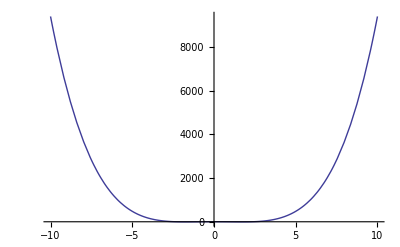

```mathematica
Plot[expr,{x,-10,10}, Epilog-> {Red,]
```

```mathematica
ZerosPlot[expr_,x_]:=(
xsolutions=Solve[expr==0,x];
ysolutions=Table[0,{Length[xsolutions]}];

Plot[
expr,{x,-10,10}
Epilog-> {PointSize-> Large}
Point/@(Transpose[
{xsolutions,ysolutions}
]/.({x->a_}-> a)
)
])
```

```mathematica
?Table
```

Table[expr,{i_max}] generates a list of i_max copies of expr. 
Table[expr,{i,i_max}] generates a list of the values of expr when i runs from 1 to i_max. 
Table[expr,{i,i_min,i_max}] starts with i=i_min. 
Table[expr,{i,i_min,i_max,di}] uses steps di. 
Table[expr,{i,{i_1,i_2,…}}] uses the successive values i_1, i_2, ….
Table[expr,{i,i_min,i_max},{j,j_min,j_max},…] gives a nested list. The list associated with i is outermost.

```mathematica
Maximize[-x^2,{x,-10,10}]
```

Maximize::ivar: -10 is not a valid variable.

```mathematica
Maximize[-x^2,x]
```

{0,{x→0}}

```mathematica
?Maximize
```

RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"].
RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"], StyleBox["y", "TI"], …. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] subject to the constraints StyleBox["cons", "TI"]. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["dom", "TI"]}], "]"}] maximizes with variables over the domain StyleBox["dom", "TI"], typically Reals or Integers.

```mathematica
MinMax[expr_, x_] := (
Solutions=Reverse[{Maximize[{expr,-10≤ x≤ 10},x], Minimize[{expr,-10≤ x≤ 10},x]},2];
Solutions =ReplaceAll[Solutions,({x-> a_}->a)];
Print[Solutions];
Plot[expr,{x,-10,10},Epilog->{{PointSize[Large]},{Map[Point,Solutions]}}]
)
```

{{10,1000},{-10,-1000}}

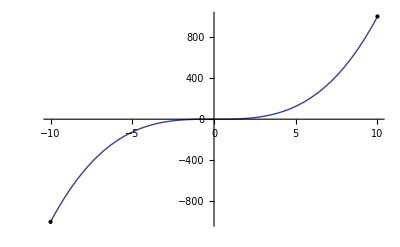

```mathematica
MinMax[x^3,x]
```

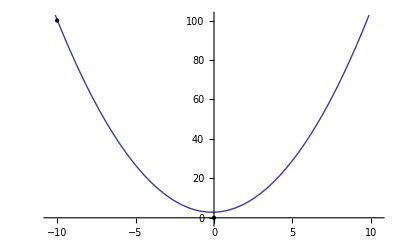

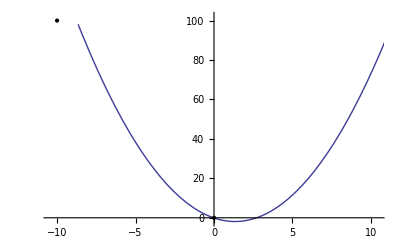

```mathematica
Minimize[{expr,-10≤ x≤ 10},x]
```

{-6,{x→-√3}}

```mathematica
?Point
```

```mathematica
Map[Point,Solutions]
```

{Point[{0,0}],Point[{100,-10}]}

Maximize::wksol: Warning: There is no maximum in the region in which the objective function is defined and the constraints are satisfied; Mathematica will return a result on the boundary.

{{0,0},{100,-10}}

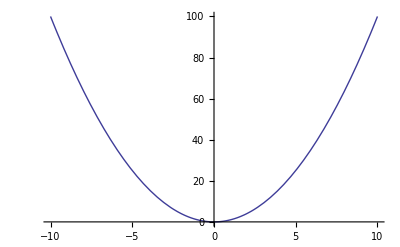
Null -Graphics-

```mathematica
MinMax[x^2,x]
```

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

```mathematica
?Maximize
```

RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", StyleBox["x", "TI"]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"].
RowBox[{"Maximize", "[", RowBox[{StyleBox["f", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] with respect to StyleBox["x", "TI"], StyleBox["y", "TI"], …. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}]}], "]"}] maximizes StyleBox["f", "TI"] subject to the constraints StyleBox["cons", "TI"]. 
RowBox[{"Maximize", "[", RowBox[{RowBox[{"{", RowBox[{StyleBox["f", "TI"], ",", StyleBox["cons", "TI"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["x", "TI"], ",", StyleBox["y", "TI"], ",", StyleBox["…", "TR"]}], "}"}], ",", StyleBox["dom", "TI"]}], "]"}] maximizes with variables over the domain StyleBox["dom", "TI"], typically Reals or Integers.

```mathematica
?Point
```

RowBox[{"Point", "[", StyleBox["coords", "TI"], "]"}] is a graphics primitive that represents a point. 
RowBox[{"Point", "[", RowBox[{"{", RowBox[{SubscriptBox[StyleBox["coords", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["coords", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], "]"}] represents a collection of points.

```mathematica
Map[Point,Solutions]
```

{Point[{0,0}],Point[{∞,-∞}]}